```mathematica
Task2AbsoluteErrors={
{1,0.327198},{4,0.104214},{16,0.0549092},{64,0.0280285},{256,0.014132},{1024,0.00709164},{4096,0.00355173},{16384,0.00177728}
};
```

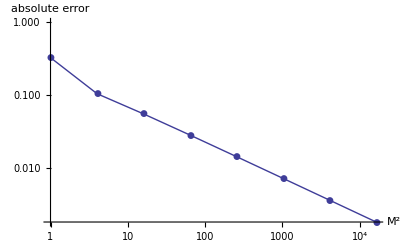

```mathematica
plotAbsError=ListLogLogPlot[Task2AbsoluteErrors, Joined->True, PlotMarkers->Automatic,AxesLabel->{"M^2","absolute error"}]
```

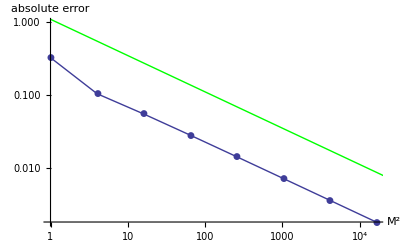

```mathematica
Show[
plotAbsError,Plot[-0.5*x+0.1,{x,0,14},PlotStyle->Green]
]
```

⇒ Convergence rate 0.5